Requires setup from ../linear-stability-analysis.nb.

### Linear stability analysis

```mathematica
params={
nD->400,nE->320,
DD->60,DE->60,Dd->0.013,Dde->0.013,
λ->6,
kD->0.1,kdD->0.1,kdE->0.15,kde->0.5,
h->0.5
};
```

#### Dispersion relation example

```mathematica
testEq=Last@nSolveHomEq[params]
```

{md→22.6954,mde→149.054,cD→56.5011,cDD→25.049,cE→21.8919}

```mathematica
dispRelSym=findDispRelSym[params,testEq,0.5];
```

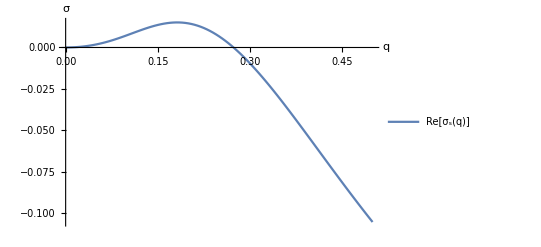

```mathematica
ListPlot[Re@dispRelSym,
Joined->True,
PlotLegends->{"Re[σ_s(q)]"},
AxesLabel->{q,σ}
]
```

#### Bulk diffusion sweep

```mathematica
data=Table[With[{
params=Join[{DD->DcIter,DE->DcIter},testParams]
},
{
DcIter,
#,
findDispRelSym[params,#,1.0]
}&@Last@nSolveHomEq[params]
],
{DcIter,5,70,5}
];//AbsoluteTiming
```

{34.4221,Null}

```mathematica
qMaxTable={#[[1]],getKeyModes[#[[3]]][[1,1,1]]}&/@data;
```

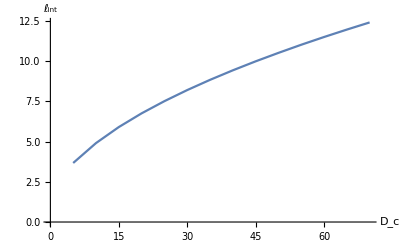

```mathematica
ListLinePlot[{
{#[[1]],Pi/#[[2]]}&/@qMaxTable
},
Joined->{True,False,False},
AxesLabel->{Subscript[D, c],Subscript[ℓ, int]},
BaseStyle->16
]
```

### Simulation data evaluation (L=500)

#### Load data

```mathematica
ClearAll@importCOMSOLData;
Options[importCOMSOLData]={"ReverseSpace"->False};
importCOMSOLData[fileName_,OptionsPattern[]]:=With[{file=OpenRead[fileName]},
With[{rawData=Table[
With[{stream=StringToStream@lines},
With[{data=ReadList[stream,Number]},
Close[stream];
data
]
],
{lines,ReadList[file,"String"]}
]},
Close@file;
If[OptionValue["ReverseSpace"]===True,
{
rawData[[All,1]],
Transpose[Partition[Transpose@Reverse@rawData[[All,2;;-1]],5],{1,3,2}]
},
{
rawData[[All,1]],
Transpose[Partition[Transpose@rawData[[All,2;;-1]],5],{1,3,2}]
}
]
]];
```

```mathematica
DcList=Range[10,60,10]
```

{10,20,30,40,50,60}

```mathematica
Do[
simData[DcIter]=importCOMSOLData[NotebookDirectory[]<>"Dc-sweep_COMSOL-data/h=2x0.5_nE=320_L=500_Dc="<>ToString[DcIter]<>"_t=2000-2100-0.5_mem-top.txt"];,
{DcIter,DcList}
];
```

#### Profile plots and kymographs

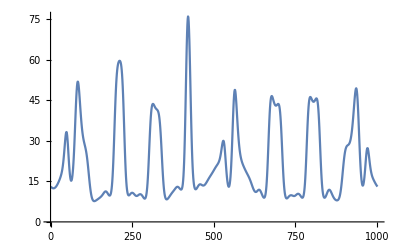

```mathematica
ListLinePlot@simData[60][[2,30,All,1]]
```

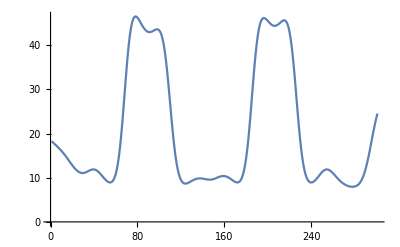

```mathematica
ListLinePlot@simData[60][[2,30,600;;900,1]]
```

```mathematica
ArrayPlot[simData[10][[2,All,All,1]],ColorFunction->"SunsetColors"]//Rasterize
```

-Graphics-

```mathematica
ArrayPlot[simData[30][[2,All,All,1]],ColorFunction->"SunsetColors"]//Rasterize
```

-Graphics-

```mathematica
ArrayPlot[simData[60][[2,All,All,1]],ColorFunction->"SunsetColors"]//Rasterize
```

-Graphics-

#### Interface width analysis

```mathematica
testData=simData[20][[2,#,All,1]](*+simData[20][[2,#,All,2]]*)&@21;
```

```mathematica
inflectionPoints=First/@findSignChangePos@Differences[testData,2];
```

```mathematica
getExtremum[list_]:=With[{
minPos=First@FirstPosition[#,Min@#]&@list,
maxPos=First@FirstPosition[#,Max@#]&@list
},
If[minPos≠1&&minPos≠Length@list,
{-1,minPos,Min@list},
If[maxPos≠1&&maxPos≠Length@list,
{1,maxPos,Max@list},
{0,0}
]]
]
```

```mathematica
findInterfaceWidths[data_,dx_]:=With[{
inflectionPoints=First/@findSignChangePos@Differences[data,2]
},
With[{
extremaList={#[[1]],getExtremum[data[[#[[1]];;#[[2]]]]]}&/@Partition[inflectionPoints,2,1]
},
First@Last@Reap@Do[
If[pair[[1,2,1]]pair[[2,2,1]]==-1,
Sow[{
dx(pair[[2,1]]+pair[[2,2,2]]-(pair[[1,1]]+pair[[1,2,2]])),
Abs[pair[[2,2,3]]-pair[[1,2,3]]]
}]
],
{pair,Partition[extremaList,2,1]}
]
]]
```

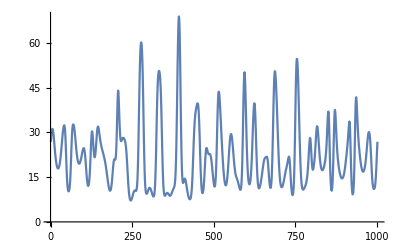

```mathematica
testData//ListLinePlot
```

```mathematica
Total[Times@@#&/@#]/Total[#[[All,2]]]&@findInterfaceWidths[testData,0.5]
```

7.71287

```mathematica
Do[interfaceWidthList[Dc]=Flatten[
findInterfaceWidths[
simData[Dc][[2,#,All,1]](*+simData[Dc][[2,#,All,2]]*)&@#,
0.5
]&/@Range[Length@simData[Dc][[2]]],
1
],
{Dc,DcList}
];
```

```mathematica
{Mean@#,StandardDeviation@#}&@(WeightedData@@Transpose[interfaceWidthList[10]])
```

{5.48377,1.71394}

```mathematica
weightedMeanInterfaceWidthTable=Table[{
Dc,
Mean@#,StandardDeviation@#
}&@(WeightedData@@Transpose[interfaceWidthList[Dc]]),
{Dc,DcList}
]
```

{{10,5.48377,1.71394},{20,7.51745,2.2663},{30,8.96912,2.75507},{40,10.2565,3.46854},{50,11.6392,4.18278},{60,12.2052,4.15129}}

```mathematica
meanInterfaceWidthTable=Table[{
Dc,
Mean[interfaceWidthList[Dc][[All,1]]],
StandardDeviation[interfaceWidthList[Dc][[All,1]]]
},
{Dc,DcList}
]
```

{{10,4.78115,1.82657},{20,6.52962,2.58058},{30,7.63552,3.25756},{40,8.66039,3.87707},{50,9.65295,4.57972},{60,10.1796,4.74474}}

### Plots (interface width as function of diffusion constant)

#### Weighted with interface amplitude

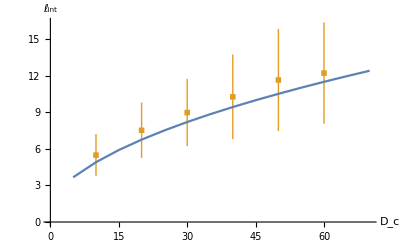

```mathematica
ListLinePlot[{
{#[[1]],Pi/#[[2]]}&/@qMaxTable,
{#[[1]],Around[#[[2]],#[[3]]]}&/@weightedMeanInterfaceWidthTable
(*{#[[1]],Around[#[[2]],#[[3]]]}&/@meanInterfaceWidthTable*)
},
Joined->{True,False,False},
PlotMarkers->{None,{Graphics[Rectangle[]],0.035}},
AxesLabel->{Subscript[D, c],Subscript[ℓ, int]},
BaseStyle->16
]
```

#### Unweighted

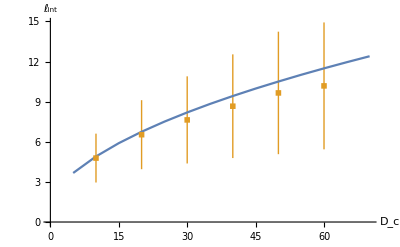

```mathematica
ListLinePlot[{
{#[[1]],Pi/#[[2]]}&/@qMaxTable,
{#[[1]],Around[#[[2]],#[[3]]]}&/@meanInterfaceWidthTable
},
Joined->{True,False,False},
PlotMarkers->{None,{Graphics[Rectangle[]],0.035}},
AxesLabel->{Subscript[D, c],Subscript[ℓ, int]},
BaseStyle->16
]
```

#### Distribution charts

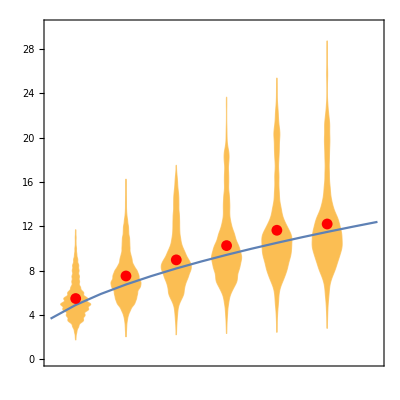

```mathematica
Show[
DistributionChart[
(WeightedData@@Transpose[interfaceWidthList[#]])&/@DcList
],
ListLinePlot[{
{#[[1]]/10,Pi/#[[2]]}&/@qMaxTable,
{#[[1]]/10,#[[2]]}&/@weightedMeanInterfaceWidthTable},
Joined->{True,False},
PlotStyle->{Default,Red}
],
FrameTicks->Automatic,
PlotRange->{0,30},
AspectRatio->1
]
```

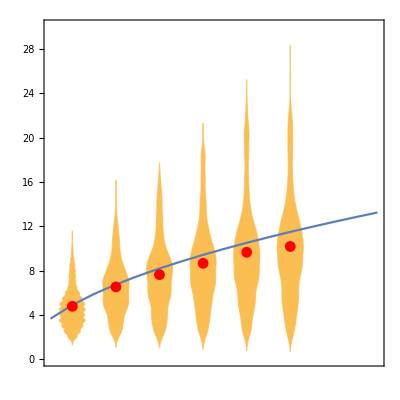

```mathematica
Show[
DistributionChart[interfaceWidthList[#][[All,1]]&/@DcList
],
ListLinePlot[{
{#[[1]]/10,Pi/#[[2]]}&/@qMaxTable,
{#[[1]]/10,#[[2]]}&/@meanInterfaceWidthTable
},
Joined->{True,False},
PlotStyle->{Default,Red}
],
FrameTicks->Automatic,
PlotRange->{0,30},
AspectRatio->1
]
```